```mathematica
Pal=RandomColor[3]
```

{RGBColor[0.07168863753791399, 0.15271925255405594, 0.8864573780036569],RGBColor[0.555210291681888, 0.4881524843588312, 0.5724516684599097],RGBColor[0.5011862970200165, 0.17904400870596437, 0.8160472664578899]}

```mathematica
Pal={RGBColor[0.2077043757885766, 0.7464871412445997, 0.8099770185280919],RGBColor[0.12442311983236554, 0.08514489930912816, 0.1561486773538463],RGBColor[0.9188083940364269, 0.1975031776090519, 0.32173246954010315]}
```

{RGBColor[0.2077043757885766, 0.7464871412445997, 0.8099770185280919],RGBColor[0.12442311983236554, 0.08514489930912816, 0.1561486773538463],RGBColor[0.9188083940364269, 0.1975031776090519, 0.32173246954010315]}

#### График отношения числа узлов с k-соседями от k при J=0

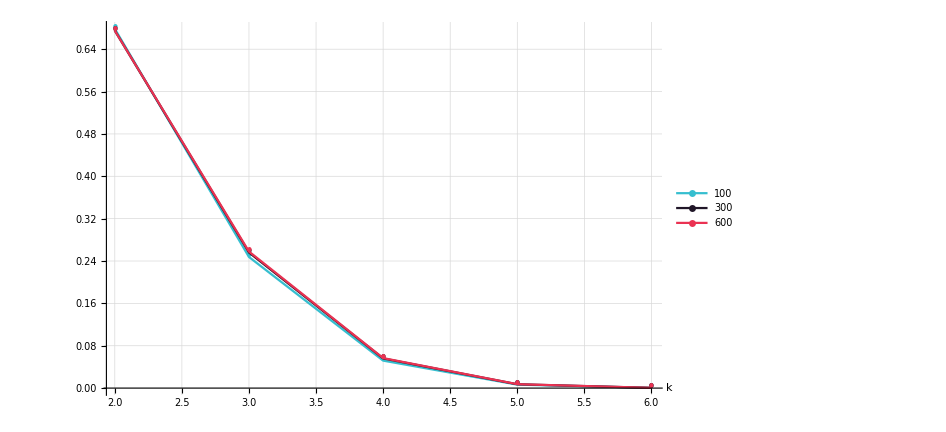

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["16.08 (Ising-ISAW, Bulk)"];
data=Import["Geometry_Ising.txt","Table"];
Needs["ErrorBarPlots`"]
data=Delete[data,1];
Ns=Union[data[[All,1]]];
Plots={};
Colors=Pal;
Do[
line=Select[data, #[[1]]==n&][[1]];
line={{{2,line[[4]]},ErrorBar[line[[5]]]},{{3,line[[6]]},ErrorBar[line[[7]]]},{{4,line[[8]]},ErrorBar[line[[9]]]},{{5,line[[10]]},ErrorBar[line[[11]]]},{{6,line[[12]]},ErrorBar[line[[13]]]}};
plt=ErrorListPlot[line, PlotLegends->{n},PlotStyle->First[Colors],PlotMarkers->Style[•,15],Joined->True];
AppendTo[Plots,plt];
Colors=Delete[Colors,1];
,{n,Ns}]
gr=Show[Plots, ImageSize->700, AxesLabel->{Style["k",15],""},TicksStyle->15,GridLines->Automatic]
SetDirectory[NotebookDirectory[]];
SetDirectory["Images"];
Export["IsingISAW_Bulk_J0.png",gr];
```

Data:
1 - N
2 - J
3 - h
4 - n2
5 - n2_err
6 - n3
7 - n3_err
8 - n4
9 - n4_err
10 - n5
11 - n5_err
12 - n6
13 - n6_err

#### Графики зависимости отношения числа узлов с k - соседями от J от k

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["16.08 (Ising-ISAW, Bulk)"];
data=Import["Geometry_Ising_All.txt","Table"];
Needs["ErrorBarPlots`"]
Ns=Union[data[[All,1]]];
PlotsAll={};
Font1=20;
Do[
Colors=Pal;
Plots={};
Do[
line=Select[data, #[[1]]==n1&];
line= Map[{{#[[2]],#[[i]]},ErrorBar[#[[i+1]]]}&,line];
plt=ErrorListPlot[line, PlotLegends->{Style[n1,Font1]},PlotStyle->First[Colors],Joined->True,PlotRange->All,AxesLabel->{Style["J",Font1],Style[Text[Subscript[n, N[i/2]]],Font1]}];
AppendTo[Plots,plt];
Colors=Delete[Colors,1];
,{n1,Ns}];
AppendTo[PlotsAll,Plots];
,{i,{4,6,8,10,12}}];
SetDirectory[NotebookDirectory[]];
SetDirectory["Images"];
i=2;
fp1=Line[{{0.52,0},{0.52,1}}];
fp2=Line[{{0.53,0},{0.53,1}}];
Do[
Export[StringJoin["IsingISAW_Bulk_n",ToString[i],".png"], Show[plt,ImageSize->700,PlotRange->All,AxesOrigin->{0,0},Epilog->{Red,Dashed,fp1,Red, Dashed,fp2}, AxesStyle->Directive[Font1]]];
i+=1;
,{plt,PlotsAll}]
Import["C:\\Users\\user\\Documents\\Wolfram Mathematica\\Проект\\Расчёты .nb\\Images\\IsingISAW_Bulk_n2.png"]
```

-Graphics-

```mathematica
Pal={RGBColor[0.2077043757885766, 0.28, 0.8099770185280919],RGBColor[0.12442311983236554, 0.08514489930912816, 0.1561486773538463],RGBColor[0.9188083940364269, 0.1975031776090519, 0.32173246954010315]};
SetDirectory[NotebookDirectory[]];
SetDirectory["16.08 (Ising-ISAW, Bulk)"];
data=Import["Geometry_Ising_All.txt","Table"];
Needs["ErrorBarPlots`"]
Ns=Union[data[[All,1]]];
PlotsAll={};
Font1=30;
Do[
Colors=Pal;
Plots={};
PS=20;
Do[
line=Select[data, #[[1]]==n1&];
line= Map[{{#[[2]],#[[i]]},ErrorBar[#[[i+1]]]}&,line];
plt=ErrorListPlot[line,PlotMarkers->{Automatic,PS},PlotStyle->First[Colors],Joined->True,Axes->{False, False}];
AppendTo[Plots,plt];
Colors=Delete[Colors,1];
,{n1,Ns}];
AppendTo[PlotsAll,Plots];
,{i,{4,6,8,10,12}}];
Font1=30;
Font2=Font1*1.3;
IS={900,600};
fp1=Line[{{0.52,0},{0.52,1}}];
fp2=Line[{{0.53,0},{0.53,1}}];
a2=Show[PlotsAll[[1]],ImageSize->IS,Frame->True,FrameStyle->Directive[Black,Font1],FrameLabel->{Style["J",Black,Font1],Style[Text[Subscript[n, 2]],Black,Font1]},Epilog->{Red,Thick,Dashed,fp1,Red, Dashed,fp2}];
a3=Show[PlotsAll[[2]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font2],FrameLabel->{Style["J",Black,Font2],Style[Text[Subscript[n, 3]],Black,Font2]},Epilog->{Red,Thick,Dashed,fp1,Red, Dashed,fp2}];
a4=Show[PlotsAll[[3]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font2],FrameLabel->{Style["J",Black,Font2],Style[Text[Subscript[n, 4]],Black,Font2]},Epilog->{Red,Thick,Dashed,fp1,Red, Dashed,fp2}];
a5=Show[PlotsAll[[4]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font2],FrameLabel->{Style["J",Black,Font2],Style[Text[Subscript[n, 5]],Black,Font2]},Epilog->{Red,Thick,Dashed,fp1,Red, Dashed,fp2}];
a6=Show[Legended[PlotsAll[[5]],Placed[Framed[LineLegend[Pal,Map[Style[#,Font1]&,Ns],LegendMarkerSize->30]],{0.1,0.8}]],ImageSize->IS,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Font1],FrameLabel->{Style["J",Black,Font1],Style[Text[Subscript[n, 6]],Black,Font1]},Epilog->{Red,Thick,Dashed,fp1,Red, Dashed,fp2}];
a=GraphicsRow[{a3,a4,a5}];
b=GraphicsRow[{a2,a6}];
SetDirectory[NotebookDirectory[]];
SetDirectory["Images"];
a=ImageCollage[{a,b},Background->None,ImageSize->1200]
Export["Ising3D_Complex.png",a];
```

-Graphics-